```mathematica
A
```

-66+281 x-179 x^2+14 x^3

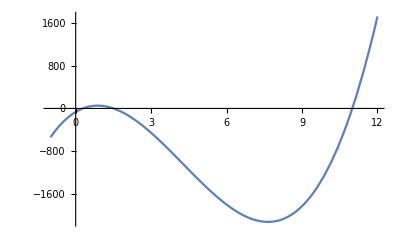

```mathematica
f[x_]=14x^3-179x^2+281x-66
Plot[f[x],{x,-1,12}]
```

```mathematica
a= 10;b = 12;
eps = 0.001;i=0;x1=b;
x0=100;line1=0;line2=0;

D[f[x],{x,2}]
f[a]
f[b]
```

-358+84 x

-1156

1722

```mathematica
While[Abs[x1-x0]>eps,
x0=x1;
x1= x0-f[x0]/(f[x0]-f[a])*(x0-a);
If[i==0 ,line1=x1];
If[i==1,line2=x1];	
i++;
]
i
Round[x1, eps]
```

6

11.

FindRoot::nlnum1: The function value {{-396.+479. x-151. x^2+14. x^3}[0.]} is not a list of numbers with dimensions {1} when the arguments are {0.}.

```mathematica
FindRoot[f[x]==0,{x,2}]
```

{x→1.5}

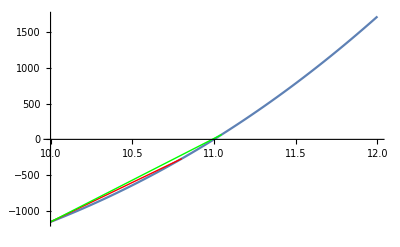

```mathematica
Show[Plot[f[x],{x,a,b}],
Graphics[{Red,Line[{{a,f[a]},{line1,f[line1]}}]}],
Graphics[{Green,Line[{{a,f[a]},{line2,f[line2]}}]}]
]
```